s/(5+s)

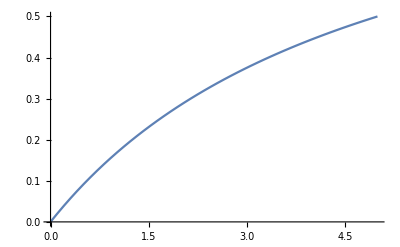

```mathematica
test[s_]=s/(1+s+4)
Plot[test[s],{s,0,5}]
```

```mathematica
func[v_]=1/(1+s+((2(δ+v/c Subscript[ω, l]))/Γ)^2)
```

1/(1+s+(4 (δ+(v ω_l)/c)^2)/Γ^2)

```mathematica
D[func[v],v]
```

-(8 ω_l (δ+(v ω_l)/c))/(c Γ^2 (1+s+(4 (δ+(v ω_l)/c)^2)/Γ^2)^2)

```mathematica
funcm[v_]=1/(1+s+((2((1+-v/c)Subscript[ω, l]-Subscript[ω, 0]))/Γ)^2)
```

1/(1+s+(4 (-ω_0+(1-v/c) ω_l)^2)/Γ^2)

```mathematica
D[funcm[v],v]
```

(8 ω_l (-ω_0+(1-v/c) ω_l))/(c Γ^2 (1+s+(4 (-ω_0+(1-v/c) ω_l)^2)/Γ^2)^2)